## Power-law

```mathematica
f0=10^-2.59 ;
M0=6.23;
α0=1.92;
i0=30;
j0=10;
```

## mass function

```mathematica
Ppower[i_,α_,M_:5]:=(α-1)/M*(i/M)^-α;
Integrate[Ppower[i,α,M],{i,M,∞},Assumptions->α>1&&M>0]
```

1

## m_pbh

```mathematica
1/Integrate[Ppower[i,α,M]/i,{i,M,∞},Assumptions->α>1&&M>0]
mpbh[α_,M_]:=(M α)/(-1+α)
```

(M α)/(-1+α)

## F(m)

```mathematica
F[i_,α_,M_]:=Ppower[i,α,M]*mpbh[α,M]/i;
F[i,α,M]
Integrate[F[i,α,M],{i,M,∞},Assumptions->α>1&&M>0]
```

((i/M)^-α α)/i

1

## R1

```mathematica
Integrate[l^(-21/37)F[l,α,M],{l,M,∞},Assumptions->α>1&&M>0]
```

(37 α)/(M^(21/37) (21+37 α))

```mathematica
1.32*10^6*(f/mpbh[α,M])^(53/37)(37 α)/(M^(21/37) (21+37 α))*(i*j)^(3/37)*(i+j)^(36/37)F[i,α,M]*F[j,α,M]//Simplify
```

(4.884×10^7 (i+j)^(36/37) (i/M)^-α (j/M)^-α ((f (-1+α))/(M α))^(53/37) α^3)/((i j)^(34/37) M^(21/37) (21+37 α))

```mathematica
Clear[i,mergerRateDensity1st]
mergerRateDensity1st[f_,i_,j_,α_,M_]:=(4.884*^7 (i+j)^(36/37) (i/M)^-α (j/M)^-α ((f (-1+α))/(M α))^(53/37) α^3)/((i j)^(34/37) M^(21/37) (21+37 α));
```

```mathematica
mergerRateDensity1st[fpbh0,i0,j0,α0,M0]
```

0.0248481

## R2

```mathematica
Integrate[l^(-42/37)*F[l,α,M],{l,M,∞},Assumptions->α>1&&M>0]
```

(37 α)/(M^(42/37) (42+37 α))

```mathematica
mergerRateDensity2nd0[f_,i_,j_,k_,α_,M_]:=1.59*10^4*(f/mpbh[α,M])^(69/37)k^(6/37)(37 α)/(M^(42/37) (42+37 α))(i+j)^(6/37)(i+j+k)^(72/37)F[i,α,M]*F[j,α,M]*F[k,α,M]
```

```mathematica
mergerRateDensity2nd0[f,i-e,e,j,α,M]
```

(588300. i^(6/37) (i+j)^(72/37) (e/M)^-α ((-e+i)/M)^-α (j/M)^-α ((f (-1+α))/(M α))^(69/37) α^4)/(e (-e+i) j^(31/37) M^(42/37) (42+37 α))

```mathematica
Integrate[mergerRateDensity2nd0[f,i-e,e,j,α,M],{e,M,i-M},Assumptions->0<2M≤i&&j>0]//Simplify
```

1/((i j)^(31/37) (42+37 α))588300. i^(-2 α) j^-α (i+j)^(72/37) M^(-3+3 α) ((f (-1+α))/α)^(69/37) α^4 (-Beta[M/i,-α,-α]+Beta[1-M/i,-α,-α])

```mathematica
Clear@mergerRateDensity2nd1;
mergerRateDensity2nd1[f_,i_,j_,α_,M_]:=If[i>2*M,1/((i j)^(31/37) (42+37 α))588300. i^(-2 α) j^-α (i+j)^(72/37) M^(-3+3 α) ((f (-1+α))/α)^(69/37) α^4 (-Beta[M/i,-α,-α]+Beta[1-M/i,-α,-α]),0];

mergerRateDensity2nd[f_,i_,j_,α_,M_:5]:=1/2*(mergerRateDensity2nd1[f,i,j,α,M]+mergerRateDensity2nd1[f,j,i,α,M])
```

```mathematica
mergerRateDensity2nd1[fpbh0,i0,j0,α0,M0]
```

0.000606604

```mathematica
mergerRateDensity2nd1[fpbh,j,i,α,M]
```

0.000857077

```mathematica
mergerRateDensity2nd[fpbh,i,j,α,M]
```

0.000428538

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,M_?NumericQ]:=mergerRateDensity2nd[f,i,j,α,M]/mergerRateDensity1st[f,i,j,α,M];
```

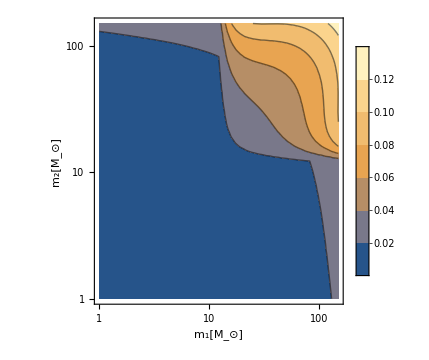

```mathematica
mMin=1;
mMax=150;

ContourPlot[ratioR[f0,i,j,α0,M0],{i,mMin,mMax},{j,mMin,mMax},FrameLabel->{"m_1[M_⊙]","m_2[M_⊙]"},ScalingFunctions->{"Log","Log"},FrameStyle->FontFamily->"Times",BaseStyle->FontSize->14,LabelStyle->GrayLevel[0],Frame->True,Axes->False,PlotRangePadding->None,ImageSize->360,AspectRatio->1,PlotLegends->Automatic]
(*Export["../latex/ratio-log.pdf",%]*)
```

```mathematica
Plot3D[{mergerRateDensity1st[f0,i,j,α0,M0]},{i,mMin,mMax},{j,mMin,mMax},PlotRange->All]
```

-Graphics3D-